```mathematica
Clear["Global`*"]

Symbol["Fast"];Symbol["Slow"];

T0=350;
nmainLBO[λ_]=Sqrt[{2.4542+0.01125/(λ^2-0.01135)-0.01388λ^2,2.5390+0.01277/(λ^2-0.01189)-0.01849λ^2+4.3025 10^-5 λ^4-2.9131 10^-5 λ^6,2.5865+0.0131/(λ^2-0.01223)-0.01862λ^2+4.5778 10^-5λ^4-3.2526 110^-5 λ^6}]+(T0-293){-(3.76λ-2.3),-(19.4-6.01λ),-(9.7-1.5λ)}10^-6 ;

nmain[λ_]=nmainLBO[λ];

refindx::unknown="The value `1` is not Slow or Fast.";
n[x_?NumberQ,y_?NumberQ,z_?NumberQ,λ_?NumberQ,fs_]:=Sort[nn/.
NSolve[Total[nn^4(nmain[λ]^2{x,y,z}^2)]-nn ^2Total[nmain[λ]^2{x,y,z}^2 {{0,1,1},{1,0,1},{1,1,0}}.(nmain[λ]^2)]+Times@@ (nmain[λ]^2)==0,nn]][[fs]]


Table[
{res,data}=
Reap[RegionPlot[Sow[{θ,φ},ccord];Sow[n[Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ],1.550,p1]/1.55+n[Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ],1.064,p2]/1.064-n[Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ],0.6309,s]/0.6309,deltan]>0,{φ,0,Pi/2},{θ,0,Pi/2},MaxRecursion->2]];


PSPoints=Sort[Select[Transpose[Transpose[data[[1]]]~Join~{data[[2]]}],Abs[#[[3]]]<10^-5&],#1[[1]]<#2[[1]]&];

Show[SphericalPlot3D[1,{θ,0,Pi/2},{φ,0,Pi/2},PlotStyle->None,Mesh->{17,17},ViewPoint->{1,1,1}],Graphics3D[{Thick,Line[{Sin[#[[1]]]Cos[#[[2]]],Sin[#[[1]]]Sin[#[[2]]],Cos[#[[1]]]}&/@PSPoints]}]],{p1,3,4},{p2,3,4},{s,3,4}]
```

{{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}}

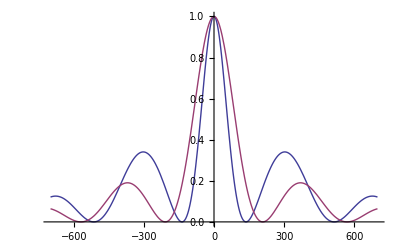

```mathematica
Clear["Global`*"]

n1=1.6;
n2=1.6;
deff=0.85 10^-12;
ε0=8.85 10^-12;
S=Pi 100^2/4 10^-12;
c=3 10^8;

k1=2 Pi/1.064 n1 10^6; 
k2=2 Pi/0.532 n2 10^6;

σ1=2 Pi k1 2 deff/ n1^2;
σ2=Pi k2 2deff/n2^2;

Δk=50;

Pout[Δk_,P0_]:=S ε0 c /2 Abs[A2[0.02]]^2/.NDSolve[{A1'[z]==-I/4/Pi  σ1 Conjugate[A1[z]]A2[z] Exp[-I Δk z],A2'[z]==-I /4/Pi σ1 A1[z]^2 Exp[I Δk z],A1[0]==Sqrt[2 P0/ε0/c/S],A2[0]==0},{A1,A2},{z,0,0.02}][[1]];

Plot[{Pout[Δk,20000]/Pout[0,20000],Pout[Δk,10000]/Pout[0,10000]},{Δk,-700,700}]
```